# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 05 — 2020-09-30 Wednesday

## Introduction to Derivatives Binomial Lattice Models of Asset Dynamics Binomial Pricing of European Options Introduction to Stochastic Calculus and Itô’s Lemma

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Arbitrage and Linear Pricing

### Type A Arbitrage and Linear Pricing

Type A arbitrage is said to exist if an investment pays an immediate payoff with no future payoff. Given two securities with prices p_1 and  p_2, The price of a portfolio of the two securities must be  p_1 +  p_2. If it were not then it would be possible, then it would be possible to buy (sell) the portfolio, break it up into its constituent assets and sell (buy) then individually, realizing an immediate riskless profit. It is hard to imagine a liquid and transparent market allowing such a situation to exist because the prices would rapidly adjust to make such a payoff impossible.

### Type B Arbitrage

A related form of arbitrage is type B arbitrage in which an investor pays nothing or a negative amount up front and has the prospect of receiving something in the future. This is equivalent to receiving a free lottery ticket.

## Introduction to Derivatives

### Derivative Securities

Derivative: A financial contract is a derivative security , or a contingent claim, if its value at expiration is exactly determined by the market price of one or more cash instruments called the underlying.

Notation

T		=	expiration date, the expiry, of the derivative

t		=	time index (typically at some time t<T)

S(t)		=	the price of the underlying at time t

F(S(t), t)	=	the derivative price at time t given S(t)

F(t)		=	F(S(t), t), when the context is clear

### Underlying Assets

Mathematica’s FinancialData[ ] function provides a uniform interface for a wide variety of data sources. However, in cases where FinancialData[ ] does not provide the necessary interface, Mathematica’s Import[ ] function is a powerful tool for “scraping” data off of web sites. Using Import[ ] for web scraping requires a bit of trial and error and the solution breaks easily if the page format changes, but it is nevertheless a powerful tool for getting data.

#### Stocks

Stocks or equities are claims against the real returns of companies. For example, here are some basic data on Microsoft:

```mathematica
FinancialData["MSFT",#]&/@{"Name","OHLCV","MarketCap"}
```

{Microsoft,{138.97 $,140.01 $,136.26 $,136.37 $,27935270 shares},1.0412407425957275e12 $}

#### Currencies

The currencies of different nations are typically “priced” in terms of exchange rates. For example, here is the Euro/US Dollar exchange rate; i.e., the number of €s it takes to “buy” a $.

```mathematica
FinancialData["EUR/USD"]
```

1.1123

```mathematica
FinancialData["JPY/EUR"]
```

0.00828981

```mathematica
FinancialData["GBP/USD"]
```

1.28727

#### Interest Rates

Interest rates are based on some notional asset, e.g., a Treasury Bill, Note or Bond. For example, here is a table of the US Treasury yield curves for the current month scraped off the US Treasury web site:

```mathematica
TableForm[Import["https://www.treasury.gov/resource-center/data-chart-center/interest-rates/Pages/TextView.aspx?data=yield",{"Data",{2,1,2}}]⟦1,1,2⟧]
```

Date | 1 mo | 2 mo | 3 mo | 6 mo | 1 yr | 2 yr | 3 yr | 5 yr | 7 yr | 10 yr | 20 yr | 30 yr
09/01/20 | 0.09 | 0.11 | 0.12 | 0.13 | 0.12 | 0.13 | 0.14 | 0.26 | 0.46 | 0.68 | 1.2 | 1.43
09/02/20 | 0.1 | 0.1 | 0.12 | 0.12 | 0.13 | 0.14 | 0.16 | 0.26 | 0.45 | 0.66 | 1.16 | 1.38
09/03/20 | 0.1 | 0.11 | 0.11 | 0.12 | 0.12 | 0.13 | 0.15 | 0.24 | 0.43 | 0.63 | 1.13 | 1.34
09/04/20 | 0.09 | 0.1 | 0.11 | 0.12 | 0.13 | 0.14 | 0.18 | 0.3 | 0.5 | 0.72 | 1.25 | 1.46
09/08/20 | 0.1 | 0.1 | 0.13 | 0.14 | 0.15 | 0.14 | 0.17 | 0.28 | 0.47 | 0.69 | 1.22 | 1.43
09/09/20 | 0.1 | 0.11 | 0.12 | 0.14 | 0.14 | 0.14 | 0.17 | 0.28 | 0.48 | 0.71 | 1.25 | 1.45
09/10/20 | 0.1 | 0.11 | 0.12 | 0.12 | 0.15 | 0.14 | 0.17 | 0.26 | 0.46 | 0.68 | 1.22 | 1.43

#### Commodities

Commodities are usually physical goods such as metals (gold, silver), agricultural goods (pork bellies, soybeans) or energy products (oil, natural gas). For example, here is the gold price scraped off the Markets Insider web site:

```mathematica
Import["https://markets.businessinsider.com/commodities/gold-price",{"Data",2,2,2,1,1}]
```

1 Troy Ounce ≈ 1,097 Ounce

#### Market Indices

Market indices are computed from the prices of a basket of securities. For example, here is the S&P 500 stock index:

```mathematica
FinancialData["^GSPC"]
```

3340.97

```mathematica
FinancialData["^DJI"]
```

27665.6

### Types of Markets

#### Cash and Carry

In a cash and carry market  traders can borrow at the risk-free rate to buy and then store and insure until expiration.

A buy-and-hold strategy is an alternative to a forward or futures contract; thus, anticipated future demand is reflected in the price and the spread between the forward or future depends only on holding costs.

#### Price Discovery

In a price discovery market it is impossible to store the underlying because it is perishable or does not yet exist, e.g., spring wheat.

Thus, the current "market" price must be "discovered" via the pricing of the derivative.

### Arbitrage & Pricing

Arbitrage is taking simultaneous positions in different assets so that one generates a riskless profit higher than the risk-free rate.

If arbitrage opportunities exist, then this drives traders to sell over-valued assets, decreasing their price, and buy under-valued assets, increasing their price. This continues until an equilibrium is reached in which no further arbitrage is possible.

Arbitrage Free Pricing - We say an asset is fairly or correctly priced if there are no arbitrage opportunities with respect to it, i.e., when its price reflects a market equilibrium.

This is a reasonable model but it is only approximately true. However, in liquid markets with freely available information it is difficult for prices to drift too far from equilibrium.

## Forward and Futures Contracts

### Forward and Futures Contracts

#### Forward Contract

A forward contract is an obligation to buy or sell an underlying asset at a specified forward price on a known future date T. Forwards are traded over-the-counter (OTC).

#### Futures Contract

A futures contract is a forward that is traded on an organized exchange. They involve standardized contract prices and expiration dates and are marked-to-market daily.

### Pricing a Forward in a Cash-and-Carry Market

Consider someone at time t who needs one unit of a commodity at time T where t<T. This can be accomplished two ways: Either buy now at price S(t) for consumption at T and forego the interest on the cash used in the purchase. Or buy a forward at F(t) for delivery at T.

Thus, in the absence of other effects these two situations produce identical results. If r(t, T) is the interest rate charged from t to T, then

S(t) + r(t, T) S(t) = F(t)

If this were not so then an arbitrage involving selling (buying) the underlying while buying (selling) the forward would exist.

If there are additional costs c(t, T), such as storage and insurance, or benefits b(t, T), such as dividend payments, associated with the underlying then

S(t) + r(t, T) S(t) –  b(t, T) + c(t, T) = F(t)

S(t) (1+ r(t, T) ) –  b(t, T) + c(t, T) = F(t)

Note that the difference between S(t) and F(t), called the spread, is not related to the uncertainty of the future price of the underlying, but the costs and benefits of a buy-and-hold strategy.

#### Example: A Commodities Contract

Suppose the spot price of gold is $360/oz., the yearly interest rate is 10% and there are no storage and insurance costs or any benefits from holding gold. The fair value of a future for delivery one year hence is

F(0) = S(0) + r(0,1) S(0) = 360 + 0.10 × 360 = $396/oz.

## Options

```mathematica
FinancialData["IBM","OHLCV"]
```

{132.55 $,134.05 $,131.61 $,133.96 $,4195803 shares}

### European Options

A European-style option on a security is the right (not obligation) to buy in a call option or to sell in a put option the security at strike price K at expiry T.

The fact that an option involves a right  means that the option only has value at expiration when there is some economic benefit associated with its exercise. Thus, the relationship between S(T) and F(T) is non-linear.

#### Pay-Off Diagrams at Expiration (t = T)

Consider a case in which a trader is long--has bought--a call with strike K = 100, then F(T) = max[S(T) – K, 0].

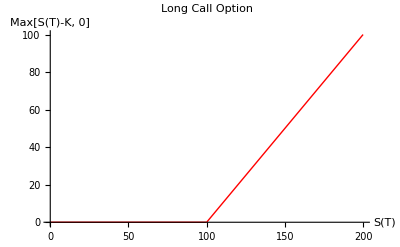

```mathematica
Plot[Max[s-100,0],{s,0,200},
PlotStyle->{Red,Thick},
PlotLabel->"Long Call Option",
AxesLabel->{"S(T)","Max[S(T)-K, 0]"}
]
```

Consider a case in which a trader is long--or has bought--a put with strike K = 100, then F(T) = max[K – S(T), 0].

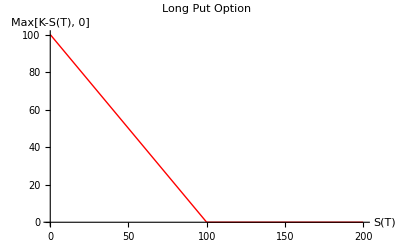

```mathematica
Plot[Max[100-s,0],{s,0,200},
PlotStyle->{Red,Thick},
PlotLabel->"Long Put Option",
AxesLabel->{"S(T)","Max[K-S(T), 0]"}
]
```

Consider a case in which a trader is short--has sold or written--a call with strike K = 100, then F(T) = – max[S(T) – K, 0].

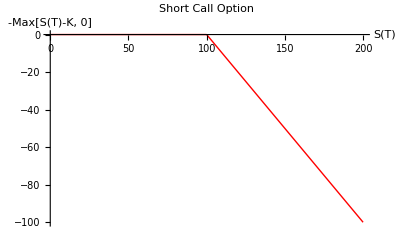

```mathematica
Plot[-Max[s-100,0],{s,0,200},
PlotStyle->{Red,Thick},
PlotLabel->"Short Call Option",
AxesLabel->{"S(T)","-Max[S(T)-K, 0]"}
]
```

Consider a case in which a trader is long--or has sold or written--a put with strike K = 100, then F(T) = – max[K – S(T), 0]

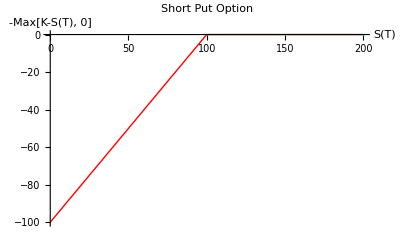

```mathematica
Plot[-Max[100-s,0],{s,0,200},
PlotStyle->{Red,Thick},
PlotLabel->"Short Put Option",
AxesLabel->{"S(T)","-Max[K-S(T), 0]"}
]
```

#### Option Valuation Prior to Expiration

An option is said to be out-of-the money if

Put:	S(t) > K

Call:	S(t) < K

An option is said to be at-the-money if S(t) = K.

An option is said to be in-the-money if

Put:	S(t) < K

Call:	S(t) > K

Prior to expiration even an out-of-the-money option has a positive premium because there is a chance that the price will drift past the strike in the time remaining to expiration.

### Swaps & Swaptions

A swap is the simultaneous selling and purchasing of cash flows involving various currencies, interest rates and a number of other financial assets.

A typical example is an interest rate swap, say, to swap a variable rate with a fixed rate. An interest rate swap could be used to effectively convert an adjustable rate loan into a fixed rate loan without renegotiating the loan or refinancing the debt.

A swaption is a contract that gives the owner the right, but not the obligation, to enter into or exit out of a swap.

Returning to interest rates. A swaption could be used to construct a situation in which a loan and swaption operates like a variable rate loan until the variable rate exceeds some trigger. The swaption is exercised  which kicks in a swap that swaps out the variable rate for a fixed rate. This strategy produces the equivalent of an adjustable rate loan with a rate ceiling.

## Binomial Lattice Models

### Geometric Binomial Lattices

A useful special case of a lattice is the binomial lattice. At each step one of the branches of a node combines with one of the branches of another. Thus, instead of 2^n leaf nodes, there are only n+1 leaves.

Let S(t) denote the price of the asset at time t. At time t + Δ with probability p_+ the asset  will be u×S[t] and with probability p_- = 1-p_+ the asset will be S[t]/u.

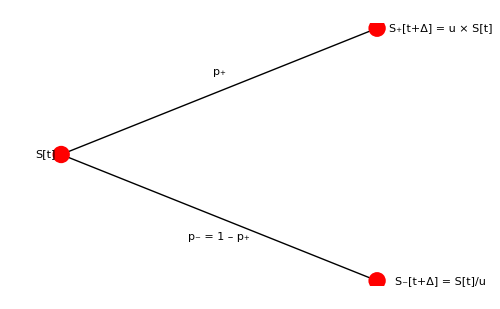

Following this model, after n up steps and m down steps the price will be u^(n-m) S[t] regardless of the specific sequence of up and down steps it took to get there. Thus, over multiple time steps the process forms a recombinant structure called a lattice.

### Example: Stock Price Model

Consider the price model above in which S(0)=1, Δ = 0.1, p_+ = 0.5, and  u_Δ = 1.1. We can plot a full ten steps on graph with time along the x-axis and price along the y-axis.

TRepresenting a lattice as a sequence of vectors, this function takes a lattice x and adds one step using the parameters p_+,Δ, and u:

```mathematica
xAddGeoStep[x_,{p_,Δ_,u_}]:=Append[x,Append[#u,Last[#]/u]&[Last[x]]];
```

With S(0)=1, represented by the root {{1}}, a single step is then

```mathematica
xAddGeoStep[{{1}},{0.5,0.01,1.1}]
```

{{1},{1.1,0.909091}}

A lattice with two steps is the recursion

```mathematica
xAddGeoStep[xAddGeoStep[{{1}},{0.5,0.01,1.1}],{0.5,0.01,1.1}]
```

{{1},{1.1,0.909091},{1.21,1.,0.826446}}

And over ten steps we can use Nest to recursively apply the function “xAddGeoStep[#,{0.5,0.01,1.1}]&”. We also Map (/@) MatrixForm to provide an easier to read output.

```mathematica
MatrixForm/@Nest[xAddGeoStep[#,{0.5,0.01,1.1}]&,{{1}},10]
```

{(1),(1.1
0.909091),(1.21
1.
0.826446),(1.331
1.1
0.909091
0.751315),(1.4641
1.21
1.
0.826446
0.683013),(1.61051
1.331
1.1
0.909091
0.751315
0.620921),(1.77156
1.4641
1.21
1.
0.826446
0.683013
0.564474),(1.94872
1.61051
1.331
1.1
0.909091
0.751315
0.620921
0.513158),(2.14359
1.77156
1.4641
1.21
1.
0.826446
0.683013
0.564474
0.466507),(2.35795
1.94872
1.61051
1.331
1.1
0.909091
0.751315
0.620921
0.513158
0.424098),(2.59374
2.14359
1.77156
1.4641
1.21
1.
0.826446
0.683013
0.564474
0.466507
0.385543)}

A plot of this lattice is

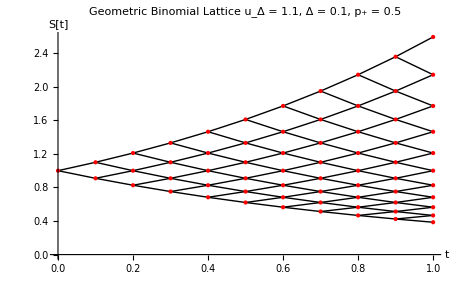

### Limiting Distribution

Consider a geometric binomial lattice as described above with n steps and each step being of duration Δ = 1/n. If we number the nodes from top to bottom in step n > 0 from 0 to n, then the probability that node i in step n is reached is determined by the binomial distribution:

ℙ_n[i]=(n/i)(p^i(1-p))^(n-i),   i ϵ {0, …, n}

A plot of the pdf at the leaf nodes for p = 0.5 , u = 1.1 and t=1 (i.e., n = 10) is:

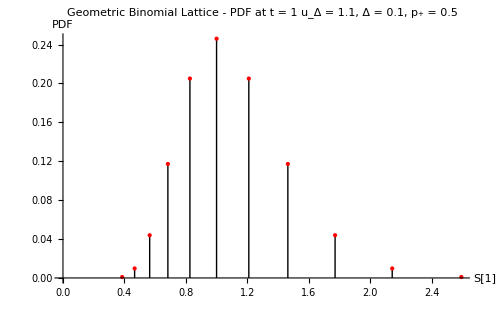

If we take the log of the x-values we get a the usual binomial distribution, something that looks very much like a discrete approximation to a Normal distribution. The plot below has the distribution of log price with a Normal distribution overlaid on it.

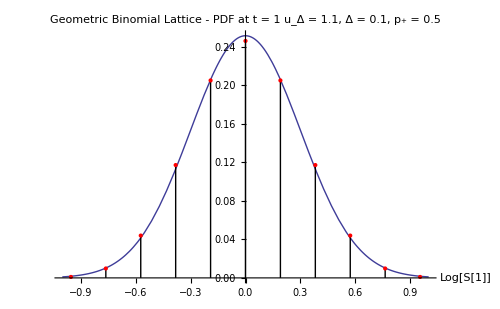

As the number of steps n → ∞ or the size of the time step Δ → 0, the distribution of log prices asymptotically approaches a Normal distribution. When log[X] is Normally distributed, then X is said to be log Normally distributed.

```mathematica
PDF[LogNormalDistribution[μ,σ],r]
```

Piecewise[{{(ⅇ^(-(-μ+Log[r])^2/(2 σ^2)))/(√(2 π) r σ), r>0}, {0, True}}]

```mathematica
TableForm[Through[{Mean,StandardDeviation,Skewness,Kurtosis}[LogNormalDistribution[μ,σ]]],TableHeadings->{{"mean","sdev","skew","kurt"}}]
```

mean | ⅇ^(μ+σ^2/2)
sdev | √(ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2)))
skew | √(-1+ⅇ^(σ^2)) (2+ⅇ^(σ^2))
kurt | -3+3 ⅇ^(2 σ^2)+2 ⅇ^(3 σ^2)+ⅇ^(4 σ^2)

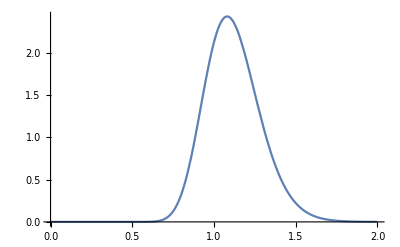

```mathematica
Plot[PDF[LogNormalDistribution[0.1,0.15],r],{r,0,2}]
```

## Finite State Models

We’ll work through a simple binomial case here with p_+, p_- > 0.

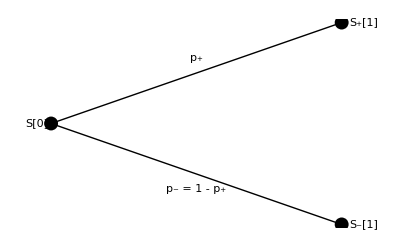

In the absence of arbitrage and in the presence of a risk-free asset we have

(1/S[0])=(1+r_f | 1+r_f
S_+[1] | S_-[1])((ψ_+)/(ψ_-)),    ((ψ_+)/(ψ_-))>(0/0)

```mathematica
Solve[{1.,100.}=={{1.02,1.02},{105.,97.}}.{ψ1,ψ2},{ψ1,ψ2}]
```

{{ψ1→0.612745,ψ2→0.367647}}

The state prices and risk neutral measure are:

```mathematica
{nPsi1,nPsi2}={ψ1,ψ2}/.First[%]
```

{0.612745,0.367647}

```mathematica
{nQ1,nQ2}={nPsi1,nPsi2}/Total[{nPsi1,nPsi2}]
```

{0.625,0.375}

Under the risk neutral measure the current price is the discounted expected value of the future price.

S(0)=(1+r_f)^-1 𝔼_𝒬[S(1)]

```mathematica
1/1.02{nQ1,nQ2}.{105.,97.}
```

100.

Note that  S_+[1]/S[0]> 1+r_f > S_-[1]/S[0] implies that ψ_+, ψ_- > 0. If that were not the case, then arbitrage opportunities would exist.

For example, if S_+[1]/S[0]>S_-[1]/S[0]>(1+r_f), then it would be possible to borrow the amount S[0] of cash and buy one unit of the asset. After one period the asset is guaranteed to make more than (1+r_f); hence, it will be possible to sell the asset, repay the borrowed cash and reap a guaranteed profit.

On the other hand, if (1+r_f)>S_+[1]/S[0]>S_-[1]/S[0], then it would be possible to place the amount S[0] of cash into a savings account and short one unit of the asset. After one period the asset is guaranteed to make less than (1+r_f); hence, it will be possible to unwind the short by buying a share in the market using savings. The cash in the savings account will be greater than S[1] and, hence, a guaranteed profit results.

## The Binomial Option Pricing Model

### General Single Step Solution

The geometric binomial model has many advantages. First, over a reasonable number of steps it represents a surprisingly realistic model of price dynamics. Second, the state price equations at each step can be expressed in a form independent of S(t) and those equations are simple enough to solve in closed form.

(1
S(t))=(ⅇ^(r Δ) | ⅇ^(r Δ)
S_+(t+Δ) | S_-(t+Δ))((ψ_+)/(ψ_-))=(ⅇ^(r Δ) | ⅇ^(r Δ)
u_Δ S(t) | S(t)/u_Δ)((ψ_+)/(ψ_-))

If we divide the bottom row by S(t), then we see that the state prices for a geometric binomial lattice are the same throughout.

(1
1)=(ⅇ^(r Δ) | ⅇ^(r Δ)
u_Δ  | 1/u_Δ)((ψ_+)/(ψ_-))

As we will see shortly, we can solve the general problem by solving a sequence of single-step problems on the lattice. That sequence of solutions can be efficiently computed because we only have to solve for the state prices once.

### Valuing an Option with One Period to Expiration

Let the current value of a stock be S(t) = 105 and let there be a call option with unknown price C(t) on the stock with a strike price of 100 that expires the next three month period. The annual risk free rate is  r = 0.04. We’ll use a single binomial step, so  Δ = 0.25 years. For the period of t to t+Δ, u_Δ = 110%; the binomial probability is p_+ =  0.50.  In the equations below, known quantities are in blue and quantities to be solved for are in red.

(1
S(t)
C(t))=(ⅇ^(r Δ) | ⅇ^(r Δ)
u S(t) | S(t)/u
max[u S(t)-K,0] | max[S(t)/u-K,0])((ψ_+)/(ψ_-))     
⇒    (1
105
C(t))≃(1.01 | 1.01
115.50 | 95.46
16.40 | 0)((ψ_+)/(ψ_-))

Note that each column in the matrix above represents a different possible future state of nature and those states collectively are all  inclusive.

Let

m	=	current prices of cash and the asset

M	=	forward state price matrix of cash and the asset

c	=	forward state price vector of the option

ψ	=	state price vector

ν	=	current option price

These equations can be summarized as

(m
v)=(M
c^T)ψ

The values of the state prices are determined by the first two rows. The state prices can then be used to calculate the option’s price based on its two outcomes.

ψ=M^-1 m    ⇒    ν=c^T ψ        ⇒      v=c^T M^-1 m

We can solve the first two equations for the state prices. Note that the quarterly rate is ⅇ^(0.25×0.04)

```mathematica
ψ=Inverse[{{ⅇ^0.01,ⅇ^0.01},{105 1.10,105/1.10}}].{1,105}
```

{0.523572,0.466478}

If we take these values and substitute them into the last row we realize a call premium of C(t) ≃ 8.11:

```mathematica
{Max[1.1 105-100,0],Max[105/1.1-100,0]}.ψ
```

8.11537

The risk neutral measure 𝒬 is:

```mathematica
q=ψ ⅇ^0.01
```

{0.528834,0.471166}

```mathematica
Total[q]
```

1.

It is remarkable but, other than meeting the requirement that 0 < p_+ < 1, the ordinary probability measure does not play a role in the solution.

### Replicating Portfolio

An alternate approach to pricing the option, one that is in a sense dual to that of risk neutral pricing, is to build a replicating portfolio. Under the Law of One Price, if the pay-offs of the replicating portfolio are identical to those of the option, then the current price of the replicating portfolio and the option must also be identical.

Let the current value of a stock be S(t) = 105 and let there be a call option with unknown price C(t) on the stock with a strike price of 100 that expires the next three-month period. The annual risk free rate is  r = 0.04. We’ll use a single binomial step, so  Δ = 0.25 years. For the period of t to t+Δ, u=110%; the binomial probability is p_+ =  0.50.

As before, in the equations below, known quantities are in blue and quantities to be solved for are in red.

Let x_B represent the cash position (The “B” is the “bank” balance.), and x_S represents the underlying position. We seek a replicating portfolio of cash and underlying x=(x_B,x_S)^T such that

(max[u S(t)-K,0]
max[S(t)/u-K,0])=(ⅇ^(r Δ) | u S(t)
ⅇ^(r Δ) | S(t)/u)(x_B/x_S)      ⇒     C(t)=(1
S(t))^T(x_B/x_S)

In terms of the linear algebra for the risk neutral approach above, we see that the result of determining the replicating portfolio ends up with the same relationship as that of the risk neutral solution. Note the matrix above is the transpose of the state-price matrix used in the risk neutral solution. Thus, using the same notation

c=M^T x    &     v=m^T x    ⇒      v=c^T M^-1 m

ψ=M^-1 m    ⇒    ν=c^T ψ        ⇒      v=c^T M^-1 m

We can solve for the replicating portfolio:

```mathematica
x=Inverse[Transpose[{{ⅇ^0.01,ⅇ^0.01},{1.1 105,105/1.1}}]].{Max[1.1 105-100,0],Max[105/1.1-100,0]}
```

{-73.0751,0.773243}

Then use the replicating portfolio to price the option:

```mathematica
{1,105}.x
```

8.11537

and get the same result as the risk neutral pricing.

### The General Binomial Option Pricing Model

We’ll return to the example above but now assume that the option expires is 3 months, but we wish to model the stock price evolution using two lattice steps;i.e., Δ = 0.125. The binomial lattice for the stock is then

```mathematica
MatrixForm/@Nest[xAddGeoStep[#,{0.5,0.125,√1.10}]&,{{105}},2]
```

{(105),(110.125
100.114),(115.5
105.
95.4545)}

Note that we have adjusted u_0.125=√(u_0.25) so that its product over the interval is the same as the single step case.

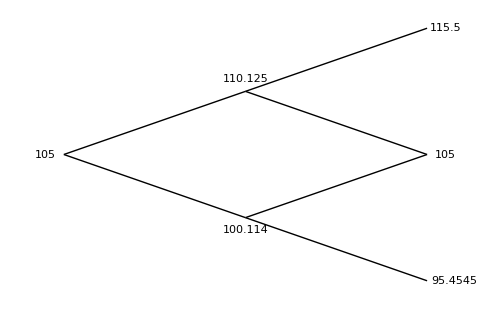

```mathematica
ψ=Inverse[{{ⅇ^0.005,ⅇ^0.005},{√1.1,1/√1.1}}].{1,1}
```

{0.537964,0.457049}

```mathematica
q=ψ ⅇ^0.005
```

{0.54066,0.45934}

The risk neutral measure is

((q_+)/(q_-))=(0.541/0.459)

The “leaves” of the lattice above occur at expiry, so for each price node we can calculate the value of the call option. This gives us a binomial pricing lattice for the option:

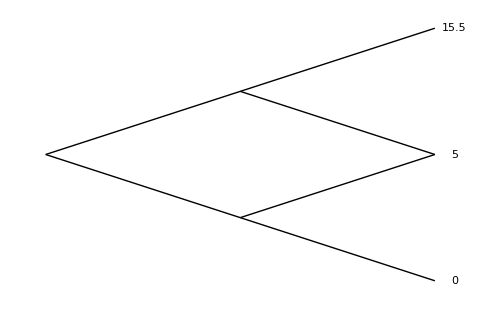

We now apply this to the next step back.

```mathematica
q.{15.5,5}/1.005
q.{5,0}/1.005
```

10.6238

2.68985

(ⅇ^(r_f Δ)((q_+)/(q_-)))^T(15.5/5.00)=(ⅇ^-0.005(0.541/0.459))^T(15.5/5.00)=10.62

(ⅇ^(r_f Δ)((q_+)/(q_-)))^T(5.00/0.00)=(ⅇ^-0.005(0.541/0.459))^T(5.00/0.00)=2.69

We can now add this information to the lattice.

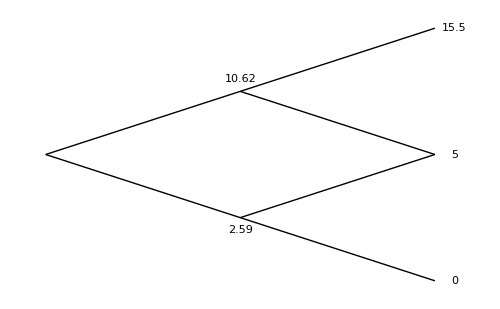

Finally, we add this to complete the lattice for the option.

```mathematica
ⅇ^-0.005 q.{10.62,2.59}
```

6.89693

(ⅇ^(r_f Δ)((q_+)/(q_-)))^T(10.62/2.59)=(ⅇ^-0.005(0.541/0.459))^T(10.62/2.59)=6.90

This allows us to complete the lattice. The value at the “root”, 6.90, is the value of the call option.

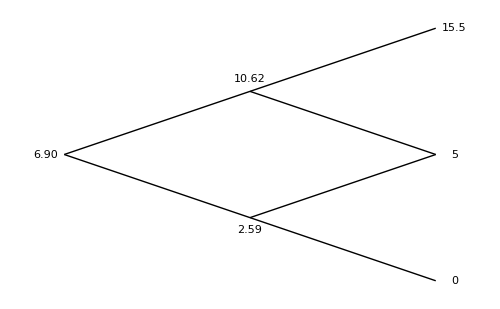

### Calibrating the Model to Market Data

For a given step-size Δ we have two free parameters in the geometric binomial model: p_+ and  u. As was shown earlier, with a sufficient number of steps the log price tends towards a Normal distribution. The calibration of the geometric binomial model at step-size Δ, therefore, involves selecting a set of parameters  p_+ and  u so that the mean and standard deviation of the log price are matched.

μ=E[log[(S(t+1))/(S(t))]]

σ^2=Var[log[(S(t+1))/(S(t))]]

p_+=1/2(1+μ/σ √Δ)

u=ⅇ^(σ √Δ)

## Mathematica Code

### Code

This code is not the most efficient; it’s meant to illustrate the computations in the simplest terms. Each step or level in the lattice is represented by a list. The entire lattice is a list of such lists, e.g., {{x11},. {x21,  x22}, {x31,  x32, x33}, ...}.

```mathematica
xLatticeForwardStep[vnOneLevel_,nUpFactor_]:=Append[vnOneLevel nUpFactor,Last[vnOneLevel]/nUpFactor];

xRiskNeutralMeasure[nRiskFree_,ΔTime_,nUpFactor_]:=(Exp[nRiskFree ΔTime]-1/nUpFactor)/(nUpFactor-1/nUpFactor);

xCallExercise[nNowPrice_,nStrikePrice_]:=Max[nNowPrice-nStrikePrice,0];

xPutExercise[nNowPrice_,nStrikePrice_]:= Max[nStrikePrice-nNowPrice,0];

xLatticeBackStep[vnOneLevel_,nRiskFree_,ΔTime_,nRiskNeutralProb_]:=
Exp[-nRiskFree ΔTime](nRiskNeutralProb Most[vnOneLevel] +(1-nRiskNeutralProb) Rest[vnOneLevel]);

xEuroCallOptGeoBin[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nRiskFree_,iIntervals_]:=Module[
{vvnBackwardTree,vnExpiryPrice,vvnForwardTree,nRiskNeutralProb,nUpFactor,ΔTime},
ΔTime=nExpiry/iIntervals;
nUpFactor=Exp[√ΔTime nVolatility];
vvnForwardTree=NestList[
xLatticeForwardStep[#,nUpFactor]&,
{nNowPrice},
iIntervals
];
nRiskNeutralProb=xRiskNeutralMeasure[nRiskFree,ΔTime,nUpFactor];
vnExpiryPrice=xCallExercise[#,nStrikePrice]&/@Last[vvnForwardTree];
vvnBackwardTree=NestList[
xLatticeBackStep[#,nRiskFree,ΔTime,nRiskNeutralProb]&,
vnExpiryPrice,
iIntervals
];
{nRiskNeutralProb,vvnForwardTree,vvnBackwardTree}
];

xEuroPutOptGeoBin[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nRiskFree_,iIntervals_]:=Module[
{vvnBackwardTree,vnExpiryPrice,vvnForwardTree,nRiskNeutralProb,nUpFactor,ΔTime},
ΔTime=nExpiry/iIntervals;
nUpFactor=Exp[√ΔTime nVolatility];
vvnForwardTree=NestList[
xLatticeForwardStep[#,nUpFactor]&,
{nNowPrice},
iIntervals
];
nRiskNeutralProb=xRiskNeutralMeasure[nRiskFree,ΔTime,nUpFactor];
vnExpiryPrice=xPutExercise[#,nStrikePrice]&/@Last[vvnForwardTree];
vvnBackwardTree=NestList[
xLatticeBackStep[#,nRiskFree,ΔTime,nRiskNeutralProb]&,
vnExpiryPrice,
iIntervals
];
{nRiskNeutralProb,vvnForwardTree,vvnBackwardTree}
];
```

### Example — Pricing Put and Call Options

Consider a stock with current price S(0)=125. It’s log mean and variance are μ = 0.10 and σ^2=0.01. There is a put option on the stock with expiry T=0.5 and a strike price K = 120. The annual risk free rate is 4%. Estimate the price of the put option using a 5-step geometric binomial option model.

```mathematica
{nRiskNeutral,vvnStockLattice,vvnOptionLattice}=xEuroPutOptGeoBin[125,0.1,120,0.5,0.04,5];
```

```mathematica
MatrixForm[{#,1-#}&[nRiskNeutral]]
MatrixForm /@ vvnStockLattice
MatrixForm /@ vvnOptionLattice
```

(0.555457
0.444543)

{(125),(129.016
121.109),(133.161
125.
117.339),(137.439
129.016
121.109
113.687),(141.855
133.161
125.
117.339
110.148),(146.412
137.439
129.016
121.109
113.687
106.719)}

{(0
0
0
0
6.31342
13.2809),(0.
0.
0.
2.79538
9.37321),(0.
0.
1.23771
5.69668),(0.
0.548019
3.20706),(0.242645
1.72317),(0.897208)}

The put is ≃ 0.90.

Warning: We’re reusing some variables... Estimate the price of the call option using a 5-step geometric binomial option model.

```mathematica
{nRiskNeutral,vvnStockLattice,vvnOptionLattice}=xEuroCallOptGeoBin[125,0.1,120,0.5,0.04,5];
```

```mathematica
MatrixForm[{#,1-#}&[nRiskNeutral]]
MatrixForm /@ vvnStockLattice
MatrixForm /@ vvnOptionLattice
```

(0.555457
0.444543)

{(125),(129.016
121.109),(133.161
125.
117.339),(137.439
129.016
121.109
113.687),(141.855
133.161
125.
117.339
110.148),(146.412
137.439
129.016
121.109
113.687
106.719)}

{(26.4124
17.4393
9.01601
1.109
0
0),(22.334
13.6401
5.47904
0.613542
0.),(18.3954
9.97218
3.30288
0.339435),(14.5924
6.97941
1.97757),(11.1634
4.73689),(8.27337)}

The call is ≃ 8.27.

We can see the convergence as the number of intervals increases.

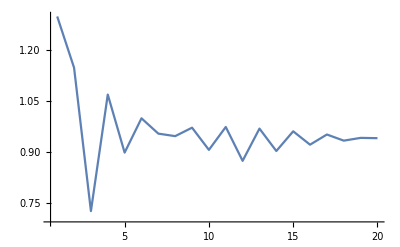

```mathematica
ListLinePlot[
Table[
{n,Last[xEuroPutOptGeoBin[125,0.1,120,0.5,0.04,n]]⟦-1,1⟧},
{n,1,20}
],
PlotRange->All
]
```

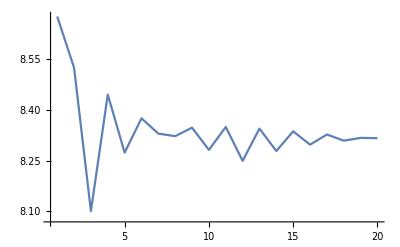

```mathematica
ListLinePlot[
Table[
{n,Last[xEuroCallOptGeoBin[125,0.1,120,0.5,0.04,n]]⟦-1,1⟧},
{n,1,20}
],
PlotRange->All
]
```

Time to expiry (T-t) = 0.5:

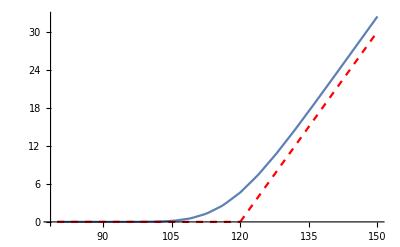

```mathematica
Show[
ListLinePlot[
Table[
{p,Last[xEuroCallOptGeoBin[p,0.1,120,0.5,0.04,20]]⟦-1,1⟧},
{p,80,150}
],
PlotRange->All
],
Plot[Max[p-120,0],{p,80,150},PlotStyle->{Red,Dashed}]
]
```

Time to expiry (T-t) = 0.1:

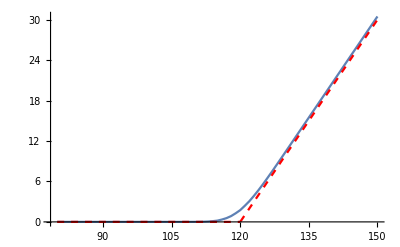

```mathematica
Show[
ListLinePlot[
Table[
{p,Last[xEuroCallOptGeoBin[p,0.1,120,0.1,0.04,20]]⟦-1,1⟧},
{p,80,150}
],
PlotRange->All
],
Plot[Max[p-120,0],{p,80,150},PlotStyle->{Red,Dashed}]
]
```

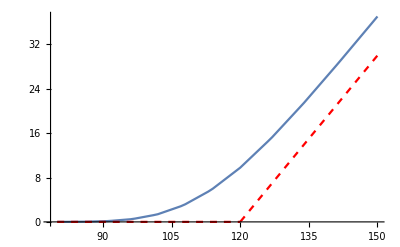

```mathematica
Show[
ListLinePlot[
Table[
{p,Last[xEuroCallOptGeoBin[p,0.1,120,1.5,0.04,20]]⟦-1,1⟧},
{p,80,150}
],
PlotRange->All
],
Plot[Max[p-120,0],{p,80,150},PlotStyle->{Red,Dashed}]
]
```

## Stochastic Calculus

### Further Development of the Binomial Model

We’ll define a standard binomial process  t ϵ [0, 1] using n steps, each of length Δ = 1/n

B(t)=B(t-Δ)+X(t) √Δ

where the X(t) are i.i.d. random variables

X(t)={+1,   with prob.  1/2
-1,   with prob.  1/2

X(t)  is not observed until the end of the interval at  t. In other words, there is no lookahead to future random events. Let

ΔB(t)=B(t)-B(t-Δ)=X(t)√Δ

At time (t – Δ) we have

𝔼[B(t)]=𝔼[ΔB(t)]+B(t-Δ)]=B(t-Δ)

Thus,  B(t) is a martingale. The ΔB(t) are called innovations because they represent new information not contained in the information available prior to t.

Note that each ΔB is i.i.d. with mean zero and variance Δ. Thus, the sum of n such innovations has mean 0 and variance n Δ=n(1/n)=1. By appealing to the Central Limit Theorem we can assert that for sufficiently large n (or small Δ) and assuming B(0) = 0

∑_(i=1)^n ΔB(i Δ)=B(1)~N[0,1]

This process is standardized so that independent of n and Δ it has a mean of zero and standard deviation of one over a unit time interval. As n → ∞, as a consequence of the Central Limit Theorem,  it approaches standard Normal distribution over that unit time interval.  Note more generally, we have for B(0) = 0 and an arbitrary t > 0

Δ → 0,    B(t)~N[0,√t]

### Geometric Binomial Process

Consider a price process

Δ S(t)=μ_S S(t-Δ)Δ  + σ_S S(t-Δ)ΔB(t)

or alternately as a return process

(Δ S(t))/(S(t-Δ))=μ_S Δ  + σ_S ΔB(t)

By specifying a mean μ_S and standard deviation σ_S we can describe a geometric diffusion process.

### Stochastic Integral

Note that summing the ΔB over the unit interval the result is a random variable.

∑_(i=1)^n ΔB(i Δ)=B(1)~N[0,1]

When Δ → 0 (n → ∞),  we can think of the limit of this process as an integral whose result is a random variable. Thus, making the substitution ΔB(t) →  ⅆB(t) as Δ → 0

lim_(Δ → 0 (or n → ∞)) ∑_(i=1)^n ΔB(i Δ) ≡ ∫_0^1 ⅆB(t) ~ N[0,1]

And this obviously generalizes to

∫_0^t ⅆB(s) ~ N[0,√t]

We have made some sense of this integral as the limit of the summation of a discrete process, but it does not quite have the same meaning as does the corresponding deterministic case because the result of the integral is a random variable.

### (ⅆB(t))^2 = ⅆt

In the deterministic case with a “smooth” function, as the step size Δ → 0 the higher powers of Δ are dominated by Δ itself. However, in the stochastic case, the limit of the binomial process we examined is not differentiable in the conventional sense: it never “smooths” out.

Now for  n steps for t from 0 to 1 of size Δ = 1 / n we have ΔB(t) = ±√Δ and, therefore, (ΔB(t))^2= Δ.

This means that as Δ → 0 we have

(ΔB(t))^2 =  Δ    ⇒     (ⅆB(t))^2= ⅆt

and

∫_0^1 (ⅆB(t))^2=∫_0^1 ⅆt=1

and, more generally,

∫_0^t (ⅆB(s))^2=∫_0^t ⅆs= t

Standard calculus is based on the notion that as Δ → 0 the higher order effects become negligible. A stochastic calculus can not make that assumption. For the class of problems we’ll be looking at, both ⅆB(t) and (ⅆB(t))^2 must be considered in order to capture both the mean and variance effects.

### The Wiener Process W(t)

Instead of a discrete binomial process, consider a continuous process W(t) such that the differences are i.i.d. random variables such that for Δ >  0

W(t) – W(t–Δ) = ΔW(t) ~ N[0, √Δ]

As before, we can divide the interval t ϵ [0, 1] into n equal steps of size Δ = 1 / n. Clearly,

∑_(i=1)^n ΔW(i Δ) ~ N[0, 1]

Unlike the binomial process B(t) which approaches a Normally distributed random variable in the limit, the equation above is a simple consequence of the fact that the increments of W(t) are i.i.d. Normal random variables whose standard deviations are the square root of the size of the increment. The random process W(t) is a called a Wiener process.

As we did with B(t) above, we can define:

lim_(Δ → 0 (or  n → ∞)) ∑_(i=1)^n ΔW(i Δ) =∫_0^1 ⅆW(t) ~ N[0,1]

As before, we have for W(0)=0 and an arbitrary t > 0

W(t)=∫_0^t ⅆW(t) ~ N[0,√t]

### (dW(t))^2 → dt in Mean Square

For the binomial process examined above we determined that (ⅆB(t))^2= ⅆt. We could do this because, for a given step size Δ, the value of (ΔB(t))^2= Δ deterministically.

For a Weiner process the value of (ΔW(t))^2 is itself a random variable; however, given that ΔW(t) is N[0, √Δ], we do know that E[(ΔW(t))^2] (i.e., the variance of  ΔW(t)) is Δ. As Δ → 0 (n → ∞) we gain more and more samples over any finite interval so Var[E[(ΔW(t))^2] → 0 over that interval. We say that (ⅆW(t))^2 →  dt in mean square as Δ → 0. In other words, the limit is not deterministic, but we can make the variance arbitrarily small by choosing a sufficiently small interval.

### Simulation Studies

We’ll illustrate these notions for the standard Wiener process W(t).

First, consider the sum ∑_(i=1)^n ΔW(i Δ) using n  = 1000 steps. As expected, W(1) ~ N[0, 1].

```mathematica
xDeltaW[n_,t_]:=Join[
{{0,0}},
Table[
{(i t)/n,RandomReal[NormalDistribution[0,√(1./n)]]},
{i,1,n}
]
];
```

```mathematica
xDeltaW[3,1]
```

{{0,0},{1/3,0.188971},{2/3,0.458512},{1,0.751913}}

```mathematica
xIntegrateTimeSeries={First/@#,Accumulate[Last/@#]}ᵀ&;
```

```mathematica
xSquareTimeSeries={First/@#,Power[Last/@#,2]}ᵀ&;
```

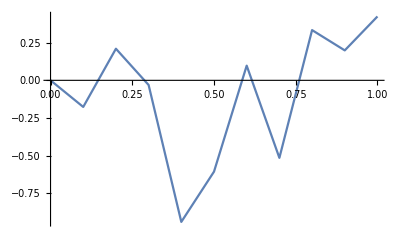

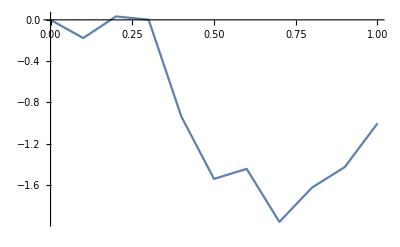

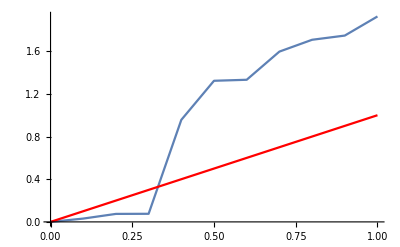

```mathematica
mnΔW=xDeltaW[10,1];
ListPlot[mnΔW,Joined->True]
ListPlot[xIntegrateTimeSeries[mnΔW],Joined->True]
Show[
ListPlot[xIntegrateTimeSeries[xSquareTimeSeries[mnΔW]],Joined->True],
Plot[x,{x,0,1},PlotStyle->Red]
]
```

Next, consider the sum ΔW(i Δ) with Δ = 1/n using 10, 100, 1000 and 10,000 steps. For each case we’ll generate 5 samples of the sum ∑_(i=1)^n (ΔW(i Δ))^m for  m = 1 and 2 over the period t ϵ [0, 1] for n time steps of  Δ = 1 / n.

As the number of steps increases the samples converge more and more closely to t. This is what you would expect with mean square convergence: The spread on the variance decreases as the number of samples increases.

```mathematica
xSimWiener[k_,n_,t_]:=Module[
{vmnΔW},
{
vmnΔW=Table[xDeltaW[n,t],{k}],
ListPlot[
xIntegrateTimeSeries/@vmnΔW,
Joined->True,
PlotStyle->Blue,
AxesLabel->{"t","ΣΔW"},
PlotLabel->ToString[k]<>" samples, Δ = "<>ToString[1./n]<>", from 0 to "<>ToString[t]
],
ListPlot[
xIntegrateTimeSeries/@(xSquareTimeSeries/@vmnΔW),
Joined->True,
PlotStyle->Blue,
PlotRange->All,
AxesLabel->{"t","Σ(ΔW)^2"},
PlotLabel->ToString[k]<>" samples, Δ = "<>ToString[1./n]<>", from 0 to "<>ToString[t]
]
}
]
```

```mathematica
r=xSimWiener[5,10,1];
```

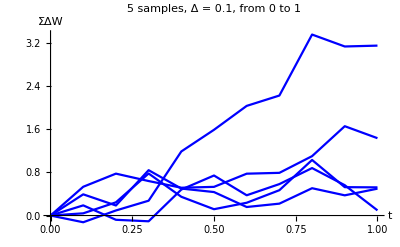

```mathematica
r[[2]]
```

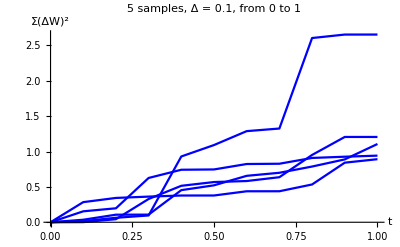

```mathematica
r[[3]]
```

```mathematica
r=xSimWiener[5,100,1];
```

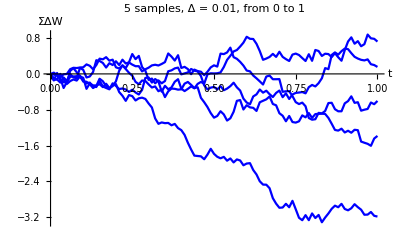

```mathematica
r[[2]]
```

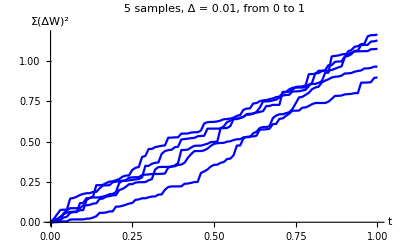

```mathematica
r[[3]]
```

```mathematica
r=xSimWiener[5,1000,1];
```

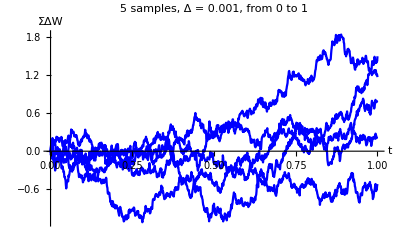

```mathematica
r[[2]]
```

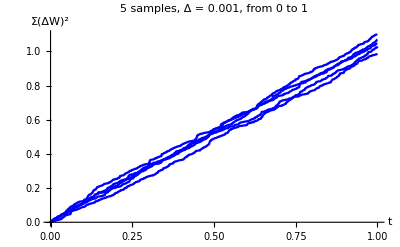

```mathematica
r[[3]]
```

```mathematica
r=xSimWiener[5,10000,1];
```

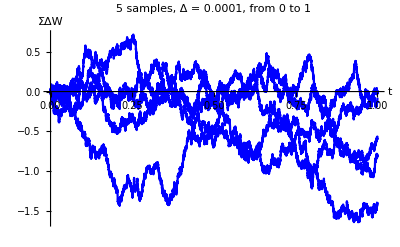

```mathematica
r[[2]]
```

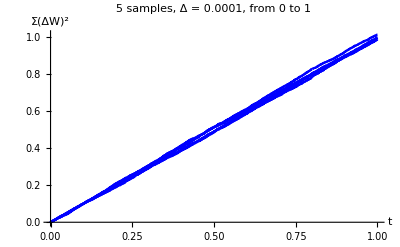

```mathematica
r[[3]]
```

## Itô Processes and Itô’s Lemma

Consider the following stochastic process, called an Itô process

ⅆX(t)=a[X(t), t]ⅆt+b[X(t), t]ⅆW(t)

The a[X(t), t]ⅆt is often called the drift term and corresponds to the local mean of the process and the b[X(t), t]ⅆW(t) the volatility term and corresponds to the local standard deviation of the process.

Consider the case of simple Brownian motion:

ⅆX(t)=μⅆt+σⅆW(t)

Then, making the simplifying assumption that X(0) = 0, we have X(t) ~ N[μ t, σ√t ]

### The Chain Rule

Consider the deterministic case

ⅆx=a[x,t]ⅆt

and a function g[x, t] which is differentiable with respect to both x and t, then if y = g[x, t] we can write ⅆy as a Taylor series

ⅆy=(((∂g)/(∂t))/((∂g)/(∂x)))^T(ⅆt/ⅆx)+1/2(ⅆt/ⅆx)^T((∂^2 g)/(∂t)^2 | (∂^2 g)/(∂t∂x)
(∂^2 g)/(∂t∂x) | (∂^2 g)/(∂x)^2)(ⅆt/ⅆx)+...

expanding this expression

ⅆy=(∂g)/(∂t)ⅆt+(∂g)/(∂x)ⅆx+1/2((∂^2 g)/(∂t)^2(ⅆt)^2+2(∂^2 g)/(∂t∂x)ⅆtⅆx+(∂^2 g)/(∂x)^2(ⅆx)^2)+...

The higher than linear order terms (i.e., those in red) in the series become negligible at sufficiently small time scales. We drop those terms and get

ⅆy=(∂g)/(∂t)ⅆt+(∂g)/(∂x)ⅆx

Substituting ⅆx=a(x,t)ⅆt into the above gives the familiar chain rule.

ⅆy=((∂g)/(∂t)+(∂g)/(∂x)a[x,t])ⅆt

### Itô’s Lemma

Consider the following Itô process:

ⅆX(t) = a[X(t), t] ⅆt + b[X(t), t] ⅆW(t)

Let g(x, t) be a function which is at least twice differentiable with respect to x and once differentiable with respect to t, then Y(t) = g[X(t), t] follows an Itô process with the same Weiner process W(t):

ⅆY(t)=((∂g)/(∂X)a+(∂g)/(∂t)+1/2(∂^2 g)/(∂X^2)b^2)ⅆt+(∂g)/(∂X)bⅆW(t)

in which the derivatives of g and the coefficients a and b depend on the arguments (X(t), t).

Proof: First, write dY(t) as a Taylor series:

ⅆY(t)=(∂g)/(∂t)ⅆt+(∂g)/(∂X)ⅆX(t)+1/2((∂^2 g)/(∂t)^2(ⅆt)^2+2(∂^2 g)/(∂t∂X(t))ⅆtⅆX(t)+(∂^2 g)/(∂X(t))^2(ⅆX(t))^2)+...

The terms in red are those which are negligible and can be dropped; the term in blue is the second order effect from the random process that, in contrast to the deterministic case, cannot be ignored.  Thus, discarding the terms that are negligible:

ⅆY(t)=(∂g)/(∂t)ⅆt+(∂g)/(∂X)ⅆX(t)+1/2(∂^2 g)/(∂X^2)(ⅆX(t))^2

Substituting ⅆX(t) and (ⅆX(t))^2 in the above

ⅆY(t)=(∂g)/(∂t)ⅆt+(∂g)/(∂X)(aⅆt+bⅆW(t))+1/2(∂^2 g)/(∂X^2)(aⅆt+bⅆW(t))^2

Expanding

ⅆY(t)=(∂g)/(∂t)ⅆt+(∂g)/(∂X)(aⅆt+bⅆW(t))+1/2(∂^2 g)/(∂X^2)((a^2(ⅆt))^2+2a b(ⅆt)( ⅆW(t))+(b^2(ⅆW(t)))^2)

And, again, discarding terms which are negligible and finally replacing (ⅆW(t))^2 with  ⅆt yields

ⅆY(t)=(∂g)/(∂t)ⅆt+(∂g)/(∂X)aⅆt+(∂g)/(∂X)bⅆW(t)+1/2(∂^2 g)/(∂X^2)b^2 ⅆt

After some simple rearrangement we have the final form above.

ⅆY(t)=((∂g)/(∂X)a+(∂g)/(∂t)+1/2(∂^2 g)/(∂X^2)b^2)ⅆt+(∂g)/(∂X)bⅆW(t)

Strictly speaking, this is not a rigorous proof; however, the approach of expanding the differential as a Taylor series, discarding the terms other than ⅆt, ⅆW(t) and (ⅆW(t))^2, and then replacing (ⅆW(t))^2with  ⅆt is one that works well for many practical problems.

Compare the deterministic and stochastic cases with additional terms in the stochastic case in blue.

ⅆy=((∂g)/(∂t)+(∂g)/(∂x)a)ⅆt

ⅆY(t)=((∂g)/(∂X)a+(∂g)/(∂t)+1/2(∂^2 g)/(∂X^2)b^2)ⅆt+(∂g)/(∂X)bⅆW(t)

#### Example

Here is one approach to implementing Itô's lemma in Mathematica. The functions must be directly coded to have the head Function. The result is the vector {ⅆt, ⅆW(t)}.

```mathematica
xIto[a_Function,b_Function,g_Function,s_Symbol,t_Symbol]:={a[s,t]D[g[s,t], s]+D[g[s,t], t]+1/2 b[s,t]^2 D[g[s,t], s,s],b[s,t]D[g[s,t], s]}
```

For the case ⅆX(t) = μ ⅆt + σ ⅆW(t),  g[x, t] = ⅇ^x, and Y(t) = g[X(t), t]:

```mathematica
xIto[Function[{s,t},μ ],Function[{s,t}, σ],Function[{s,t},Exp[s]],x,t]
```

{ⅇ^x μ+(ⅇ^x σ^2)/2,ⅇ^x σ}

Thus,

ⅆX(t)=μ ⅆt+σ ⅆW(t)
Y(t)=g[X(t),t]=ⅇ^x }   ⟹    ⅆY(t)=(μ +σ^2/2) ⅇ^(X(t)) ⅆt+σ ⅇ^(X(t)) ⅆW(t)

and substituting ⅇ^(X(t))→Y(t) we end up with the final form in terms of Y(t)

ⅆY(t)=(μ +σ^2/2)Y(t) ⅆt+σ Y(t) ⅆW(t)

## A Simple Stock Model

We can apply the above to model constant coefficient geometric Brownian motion of a stock price S(t)

ⅆS(t) = μ S(t) ⅆt + σ S(t) ⅆW(t)

Sometimes this is expressed in terms of the instantaneous rate of return of the stock. Dividing both sides by S(t)

(ⅆS(t))/(S(t))=μ ⅆt+σⅆW(t)

Note that our earlier experiments with the geometric binomial lattice (which in the limit is the same at the price model above) it appeared that the log price was Normally distributed. Let S follow the constant-coefficient geometric process above with S(0) = 1. Take g[S(t), t] = log S(t) and apply Itô’s lemma then we get

```mathematica
xIto[Function[{s,t},s μ],Function[{s,t},s σ],Function[{s,t},Log[s]],s,t]
```

{μ-σ^2/2,σ}

You can also specify the function using “&” notation.

```mathematica
xIto[μ #&,σ #&,Log[#]&,s,t]
```

{μ-σ^2/2,σ}

Thus, we have

ⅆ log S(t)=(μ-1/2 σ^2)ⅆt+σ ⅆW(t)

Thus, log S(t) is Normally distributed with a mean of  (μ-1/2 σ^2) t and a standard deviation of σ√t. It is also clear that S(t) is log Normally distributed and

log S(t)=(μ-1/2 σ^2)t+σ W(t)    ⟹    S(t)=S(0)ⅇ^((μ-1/2 σ^2)t+σ W(t))